```mathematica
(*css zebrafinch model*)
(*recursions*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs((1-lsO-lsV) vI z +lsO qO + lsV qV) + nh vh((1-lhO-lhV) vI z +lhO qO + lhV qV);
NNn :=ns vs((1-lsO-lsV) vI (1-z)+lsO(1- qO) + lsV (1-qV)) + nh vh((1-lhO-lhV) vI (1-z)+lhO(1- qO) + lhV(1- qV));
qO := (1-u)(Na/(Na +Nn));
qV:= (1-u)(Na ba/(Na ba +Nn bn));
```

```mathematica
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs((1-lsO-lsV) vI z +lsO qO + lsV qV), vh((1-lhO-lhV) vI z +lhO qO + lhV qV), 0, 0}, {vs((1-lsO-lsV) vI (1-z)+lsO(1- qO) + lsV (1-qV)), vh((1-lhO-lhV) vI (1-z)+lhO(1- qO) + lhV(1- qV)), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=Simplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=Simplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
Fasols=Solve[FFa==Fa,Fa];
```

```mathematica
test = {lsO-> 0.2 ,lhO-> 0.4 , lhV -> 0.1 , lsV -> 0};
subs = {ba->3,bn->1,z->0.6,vs->0.6,vh->0.9,vI->0.6  ,u->0.1, pa-> 0, pn-> 1};
```

```mathematica
Fasols[[2,1,2]]/.subs/.test (*check it is stable qhat with values, select positive q-hat*)
 Fasols/.subs
```

0.573474+0. ⅈ

{{Fa→-(-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)/(3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV))-(2^(1/3) (-(-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^2+3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)))/(3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (-2 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^3-27 (0.216-0.216 lsO-0.216 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV)^2+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)+√(4 (-(-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^2+3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV))^3+(-2 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^3-27 (0.216-0.216 lsO-0.216 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV)^2+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV))^2))^(1/3))+(-2 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^3-27 (0.216-0.216 lsO-0.216 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV)^2+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)+√(4 (-(-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^2+3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV))^3+(-2 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^3-27 (0.216-0.216 lsO-0.216 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV)^2+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV))^2))^(1/3)/(3 2^(1/3) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV))},{Fa→-(-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)/(3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV))+((1+ⅈ √3) (-(-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^2+3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)))/(3 2^(2/3) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (-2 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^3-27 (0.216-0.216 lsO-0.216 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV)^2+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)+√(4 (-(-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^2+3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV))^3+(-2 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^3-27 (0.216-0.216 lsO-0.216 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV)^2+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV))^2))^(1/3))-((1-ⅈ √3) (-2 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^3-27 (0.216-0.216 lsO-0.216 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV)^2+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)+√(4 (-(-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^2+3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV))^3+(-2 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^3-27 (0.216-0.216 lsO-0.216 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV)^2+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV))^2))^(1/3))/(6 2^(1/3) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV))},{Fa→-(-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)/(3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV))+((1-ⅈ √3) (-(-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^2+3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)))/(3 2^(2/3) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (-2 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^3-27 (0.216-0.216 lsO-0.216 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV)^2+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)+√(4 (-(-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^2+3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV))^3+(-2 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^3-27 (0.216-0.216 lsO-0.216 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV)^2+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV))^2))^(1/3))-((1+ⅈ √3) (-2 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^3-27 (0.216-0.216 lsO-0.216 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV)^2+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)+√(4 (-(-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^2+3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV))^3+(-2 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV)^3-27 (0.216-0.216 lsO-0.216 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV)^2+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV))^2))^(1/3))/(6 2^(1/3) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV))}}

```mathematica
QHAT= Simplify[Fasols[[2,1,2]]/.subs];
```

1/(12 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV))(1.872+2.376 lhO-17.064 lhV-2.928 lsO+5.712 lsV-((20.7283+35.9025 ⅈ) (0.787585+1. lhO^2+1.44665 lhV^2+0.175089 lsO+0.0835182 lsO^2+lhO (-1.64103-0.424672 lhV-0.401119 lsO-0.769782 lsV)+lhV (-0.726456+0.612706 lsO-0.394029 lsV)+1.0873 lsV-0.0141444 lsO lsV+0.0441311 lsV^2))/(42.5153 (0.933333-1. lhO+0.8 lhV+0.222222 lsO-0.177778 lsV)^2 (-1.+1. lsO+1. lsV)+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)+0.419169 (0.787879+1. lhO-7.18182 lhV-1.23232 lsO+2.40404 lsV)^3+√(4 (3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)-0.352836 (0.787879+1. lhO-7.18182 lhV-1.23232 lsO+2.40404 lsV)^2)^3+(42.5153 (0.933333-1. lhO+0.8 lhV+0.222222 lsO-0.177778 lsV)^2 (-1.+1. lsO+1. lsV)+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)+0.419169 (0.787879+1. lhO-7.18182 lhV-1.23232 lsO+2.40404 lsV)^3)^2))^(1/3)+ⅈ 2^(2/3) (ⅈ+√3) (42.5153 (0.933333-1. lhO+0.8 lhV+0.222222 lsO-0.177778 lsV)^2 (-1.+1. lsO+1. lsV)+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)+0.419169 (0.787879+1. lhO-7.18182 lhV-1.23232 lsO+2.40404 lsV)^3+√(4 (3 (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)-0.352836 (0.787879+1. lhO-7.18182 lhV-1.23232 lsO+2.40404 lsV)^2)^3+(42.5153 (0.933333-1. lhO+0.8 lhV+0.222222 lsO-0.177778 lsV)^2 (-1.+1. lsO+1. lsV)+9 (-0.468-0.594 lhO+4.266 lhV+0.732 lsO-1.428 lsV) (-2.52+2.7 lhO-2.16 lhV-0.6 lsO+0.48 lsV) (0.828-0.972 lhO-0.972 lhV+0.084 lsO+1.164 lsV)+0.419169 (0.787879+1. lhO-7.18182 lhV-1.23232 lsO+2.40404 lsV)^3)^2))^(1/3))

```mathematica
AA2=AA/.{Na->QH,Nn->(1-QH)}/.subs;
```

```mathematica
LL=Eigenvalues[AA2];
```

```mathematica
LL1 = LL/.QH -> QHAT/.subs /.test
```

$Aborted

```mathematica
(*isolate dominant eigenvalue*)
Lambda[ lsO_, lhO_]:=LL[[1]];
```

```mathematica
(*use Lambda1 for general soln with pa and pn as parameters*)
DlsO=D[Lambda[lsO, lhO],lsO]/.subs;
```

```mathematica
DlhO=D[Lambda[lsO, lhO],lhO] /.subs;
```

```mathematica
(*try and graph*)

lsOstart=0.01;
lhOstart=0.01;
imax=1000;
lsItab=Table[0,{i,imax}];
lhItab=Table[0,{i,imax}];
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
delta=0.04;
lsOtab[[1]]=lsOstart;
lhOtab[[1]]=lhOstart;

DlsOtab[[1]]=DlsO/.subs/.{lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.subs/.{lsO->lsOstart,lhO->lhOstart};
```

```mathematica
For[i=2,i<imax,i++,{

lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

DlsOtab[[i]]=DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
}];
```

```mathematica
lsItab = 1-lsOtab;
lhItab = 1-lhOtab;
```

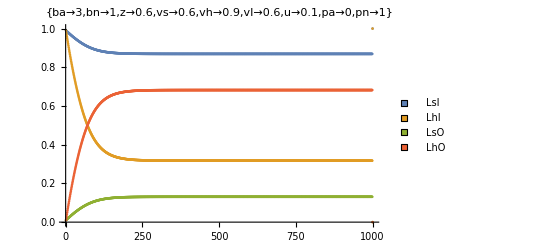

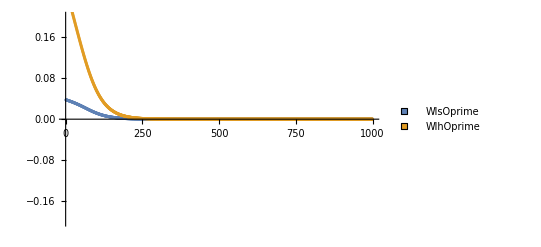

```mathematica
ListPlot[{lsItab,lhItab,lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLabel->subs, PlotLegends->PointLegend[{LsI,LhI,LsO,LhO},LegendMarkers->Graphics[Rectangle[]]]] 
ListPlot[{DlsOtab,DlhOtab},PlotRange->{All,{-0.2,0.2}},PlotLegends->PointLegend[{WlsOprime,WlhOprime},LegendMarkers->Graphics[Rectangle[]]]]
```